```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
simplexPlot[func_,plotFunc_]:=Module[{A,B,p2r,r2p,p1,p2,p3,e,x1,x2,w,h,marg,y1,y2,valid},A=Sqrt[2/3] {Cos[#],Sin[#],Sqrt[1/2]}&/@Table[Pi/2+2 Pi/3+2 k Pi/3,{k,0,2}]//Transpose;
B=Inverse[A];
(*map 3d probability vector into 2d vector*)p2r[{x_,y_,z_}]:=Most[A.{x,y,z}];
(*map 2d vector in 3d probability vector*)r2p[{u_,v_}]:=B.{u,v,Sqrt[1/3]};
(*Bounds to center the simplex*){p1,p2,p3}=Transpose[A];
(*extra padding to use*)e=1/20;
x1=First[p1]-e/2;
x2=First[p2]+e/2;
w=x2-x1;
h=p3[[2]]-p2[[2]];
marg=(w-h+e)/2;
y1=p2[[2]]-marg;
y2=p3[[2]]+marg;
valid=Function[{x,y},Min[r2p[{x,y}]]≥0&&Max[r2p[{x,y}]]≤1];
plotFunc[func@@r2p[{x,y}],{x,x1,x2},{y,y1,y2},MeshFunctions->{#3&},PlotPoints->30,RegionFunction->valid,PlotRange->Full,Axes->False]];

axes[x_,y_,z_,f_,a_]:=Graphics3D[Join[{Arrowheads[a]},Arrow[{{0,0,0},#}]&/@{{x,0,0},{0,y,0},{0,0,z}},{Text[Style["x",FontSize->Scaled[f]],{1.1*x,0*y,0*z}],Text[Style["y",FontSize->Scaled[f]],{0 x,1.1*y,0*z}],Text[Style["z",FontSize->Scaled[f]],{0*x,0*y,1.1*z}]}]]

t=AffineTransform[{{{-(1/Sqrt[2]),-(1/Sqrt[6]),1/Sqrt[3]},{1/Sqrt[2],-(1/Sqrt[6]),1/Sqrt[3]},{0,Sqrt[2/3],1/Sqrt[3]}},{1/3,1/3,1/3}}];
graphics=simplexPlot[5 Sin[#1 #2 #3]&,Plot3D];
shape=Cases[graphics,_GraphicsComplex];
gr=Graphics3D[{Opacity[.5],GeometricTransformation[shape,t]},Axes->False,Boxed->False,Lighting->"Neutral"];
pic=Show[gr,axes[1,1,1,0.05,0.02]]
```

-Graphics3D-

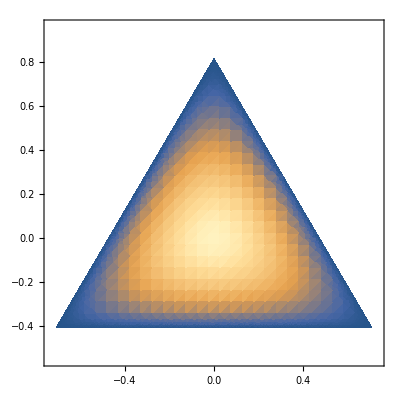

```mathematica
simplexPlot[Sin[#1 #2 #3]&,DensityPlot]
```